### Categorization

Tutorial

EcoEvo Package

EcoEvo`

EcoEvo/tutorial/Two-TraitLotka-Volterra

### Keywords

Details

# Two-Trait Lotka-Volterra

The two-trait Lotka-Volterra competition extends the trait-based Lotka-Volterra competition model to two traits.

dn_i/dt = (k[x_i,y_i]-∑_j^Nsp[1] a[x_i,y_i,x_j,y_j]n_j)n_i

k[x_i,y_i] describes the trait-dependence of the carrying capacity and a[x_i,y_i,x_j,y_j] describes how the strength of competition depends on the difference between species traits.

```mathematica
Needs["EcoEvo`"]
```

EcoEvo Package Version 0.9.0α (May 14, 2018)

Set up model.

```mathematica
SetModel[{
Guild[1]->{Variable->n,Equation->g,Trait[1]->{Variable->x,Range->Interval[{-1,1}]},
Trait[2]->{Variable->y,Range->Interval[{-1,1}]}}
}]
```

```mathematica
g[i_]:=(k[Subscript[x, i],Subscript[y, i]]-Sum[a[Subscript[x, i],Subscript[x, j],Subscript[y, i],Subscript[y, j]]*Subscript[n, j][t],{j,Nsp[1]}])*Subscript[n, i][t];
a[xi_,xj_,yi_,yj_]:=E^(-1/2*((xi-xj)^2+(yi-yj)^2)/σ^2);
k[x_,y_]:=1-(x^2+y^2);
```

Plot density-independent growth rate and competition kernel.

```mathematica
Plot3D[{k[x,y],0},{x,-1.2,1.2},{y,-1.2,1.2}]
```

-Graphics3D-

```mathematica
σ=0.8;
Plot3D[a[x,0,y,0],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

Let's start with some analytical work.

```mathematica
Clear[σ]
```

Find the one-species ecological equilibria, then solve for one-species evolutionary equilibria.

```mathematica
eq1=SolveEcoEq[{Nsp[1]->1}]⟦-1⟧
```

{n_1→1-x_1^2-y_1^2}

```mathematica
evoeq=SolveEvoEq[eq1]
```

{{x_1→0,y_1→0}}

Now check convergence stability with EvoEigenvalues and evolutionary stability with DInv.

```mathematica
EvoEigenvalues[evoeq⟦1⟧,eq1]
```

{-2,-2}

```mathematica
DInv[evoeq⟦1⟧,eq1,{{Subscript[x, 0],Subscript[y, 0]},2},Species->1]//MatrixForm
```

(-2+1/σ^2 | 0
0 | -2+1/σ^2)

As in the one-trait Lotka-Volterra competition model, the one-species evolutionary equilibrium is convergence stable (both evoeigenvalues are negative) and evolutionarily stable when σ>1/√2=0.707107.

Now let's set σ=0.8 so there is a one-species ESS and proceed with numerical analysis.

```mathematica
σ=0.8;
```

Simulate the ecological dynamics of a single species.

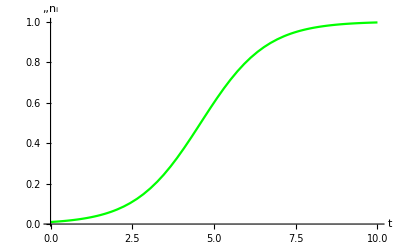

```mathematica
sol=EcoSim[{Subscript[x, 1]->0,Subscript[y, 1]->0},{Subscript[n, 1]->0.01},10];
PlotDynamics[sol]
```

Now consider an array of species along both trait axes.

```mathematica
traits=RuleList[{x,y},{19,19},{{-0.9,0.9},{-0.9,0.9}}];
ics=RuleList[n,19^2,0.0001];
sol=EcoSim[traits,ics,10^3];
PlotDynamics[sol]
```

-Graphics-

```mathematica
ListPlot3D[Table[{Subscript[x, i],Subscript[y, i],Subscript[n, i]},{i,19^2}]/.traits/.Slice[sol,10^3],Mesh->None,InterpolationOrder->0,Filling->Axis,FillingStyle->Darker@Green,PlotStyle->Green,PlotRange->{10^-4,1.0001},AxesLabel->{x,y,n}]
```

-Graphics3D-

Find a one-species eco-evolutionary equilibrium, first analytically with SolveEvoEq, then numerically with FindEcoEvoEq.

```mathematica
eq1=SolveEcoEq[{Nsp[1]->1}]⟦-1⟧
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{n_1→1.-1. x_1^2-1. y_1^2}

```mathematica
SolveEvoEq[eq1]
```

{{x_1→0,y_1→0}}

```mathematica
eeq=FindEcoEvoEq[{Subscript[x, 1]->0.1,Subscript[y, 1]->0.1,Subscript[n, 1]->0.9}]
```

{n_1→1.,x_1→0,y_1→0}

Plot the resulting invasion fitness landscape.

```mathematica
Plot3D[{Evaluate[Inv[eeq]],0},{Subscript[x, 0],-1,1},{Subscript[y, 0],-1,1},MeshFunctions->{#3&},Mesh->{40,False},PlotPoints->50,PlotStyle->{Orange,{Black,Opacity[0.2]}},AxesLabel->{Subscript[x, 0],Subscript[y, 0],inv}]
```

-Graphics3D-

Looks like a global ESS.  Check with GlobalESSQ.

```mathematica
GlobalESSQ[eeq]
```

{{True},{{-2.61754×10^-17,{x→-2.21867×10^-9,y→4.61008×10^-9}}}}

Simulate eco-evolutionary dynamics with EcoEvoSim.

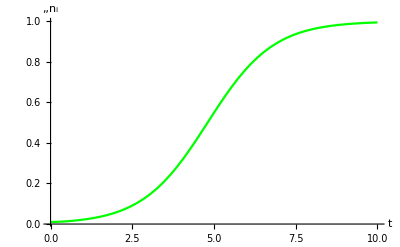

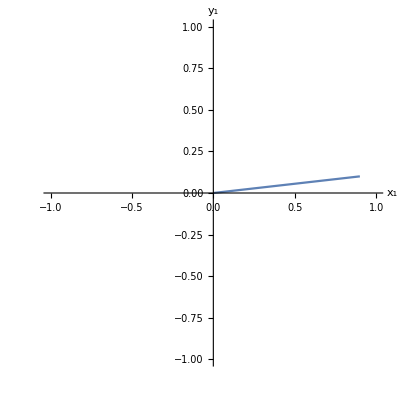

```mathematica
tmax=10;
sol=EcoEvoSim[{Subscript[x, 1]->0.9,Subscript[y, 1]->0.1},{Subscript[n, 1]->0.01},tmax];
PlotDynamics[sol,n]
ParametricPlot[{Subscript[x, 1][t],Subscript[y, 1][t]}/.sol,{t,0,tmax},PlotRange->{{-1,1},{-1,1}},AxesLabel->{Subscript[x, 1],Subscript[y, 1]}]
```

Changing the trait variance-covariance matrix affects the evolutionary path, but not the end point.

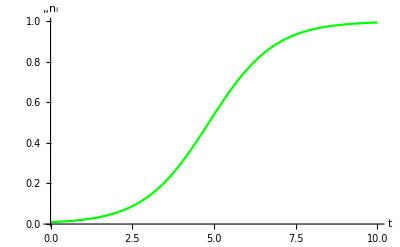

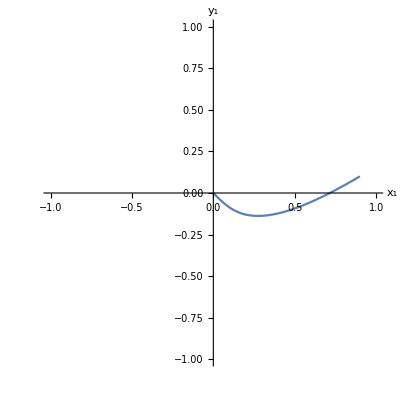

```mathematica
tmax=10;
sol=EcoEvoSim[{Subscript[x, 1]->0.9,Subscript[y, 1]->0.1},{Subscript[n, 1]->0.01},{G[1]->{{1,0.5},{0.5,1}}},tmax];
PlotDynamics[sol,n]
ParametricPlot[{Subscript[x, 1][t],Subscript[y, 1][t]}/.sol,{t,0,tmax},PlotRange->{{-1,1},{-1,1}},AxesLabel->{Subscript[x, 1],Subscript[y, 1]}]
```

Summarize the single-species dynamics with PlotEvoPhasePlane, which combines PlotZIP, PlotEvoStreams and PlotEvoIsoclines.

```mathematica
eq1=SolveEcoEq[{Nsp[1]->1}]⟦-1⟧;
PlotEvoPhasePlane[eq1,{Subscript[x, 1],-1,1},{Subscript[y, 1],-1,1}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-Graphics-

```mathematica
eq1=SolveEcoEq[{Nsp[1]->1}]⟦-1⟧;
PlotEvoPhasePlane[eq1,{G[1]->{{1,0.5},{0.5,1}}},{Subscript[x, 1],-1,1},{Subscript[y, 1],-1,1}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-Graphics-

Reducing σ leads to a branching point at {x_1→0,y_1→0}.

```mathematica
σ=0.5;
```

```mathematica
eeq=FindEcoEvoEq[{Subscript[x, 1]->0.1,Subscript[y, 1]->0.1,Subscript[n, 1]->0.9}]
```

{n_1→1.,x_1→0,y_1→0}

```mathematica
Plot3D[{Evaluate[Inv[eeq]],0},{Subscript[x, 0],-1,1},{Subscript[y, 0],-1,1},MeshFunctions->{#3&},Mesh->{40,False},PlotPoints->50,PlotStyle->{Orange,{Black,Opacity[0.2]}},AxesLabel->{Subscript[x, 0],Subscript[y, 0],inv}]
```

-Graphics3D-

Check local convergence stability with EvoEigenvalues.

```mathematica
EvoEigenvalues[eeq]
```

{-2,-2}

Negative EvoEigenvalues indicates convergence stability.

Check local evolutionary stability with DInv.

```mathematica
DInv[eeq,{{Subscript[x, 0],Subscript[y, 0]},2},Species->1]
```

{{2.,0},{0,2.}}

Positive second derivatives of fitness indicate non-ESS.

Check global evolutionary stability with GlobalESSQ.

```mathematica
GlobalESSQ[eeq]
```

{{False},{{0.153426,{x→0.526918,y→0.262548}}}}

Simulate branching with EcoEvoSim.

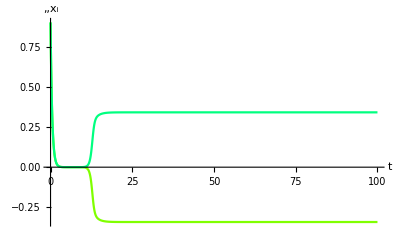

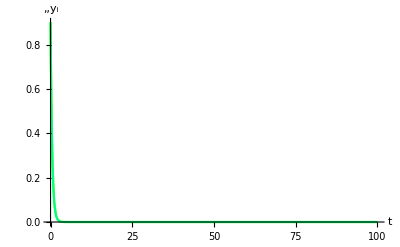

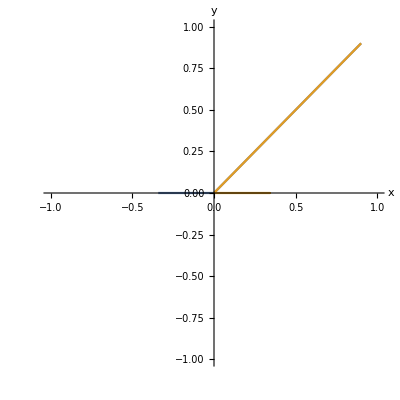

```mathematica
tmax=100;
sol=EcoEvoSim[{Subscript[x, 1]->0.9,Subscript[y, 1]->0.9,Subscript[x, 2]->0.9001,Subscript[y, 2]->0.9},{Subscript[n, 1]->0.01,Subscript[n, 2]->0.01},tmax];
PlotDynamics[sol,x]
PlotDynamics[sol,y]
ParametricPlot[Evaluate[Table[{Subscript[x, i][t],Subscript[y, i][t]},{i,2}]/.sol],{t,0,tmax},PlotRange->{{-1,1},{-1,1}},AxesLabel->{x,y}]
```

Look at the invasion fitness landscape at the end of the simulation.

```mathematica
Show[
Plot3D[{Evaluate[Inv[FinalSlice[sol]]],0},{Subscript[x, 0],-1,1},{Subscript[y, 0],-1,1},MeshFunctions->{#3&},Mesh->{40,False},PlotPoints->50,PlotStyle->{Orange,{Black,Opacity[0.2]}},AxesLabel->{Subscript[x, 0],Subscript[y, 0],inv}],
ListPointPlot3D[Table[{Subscript[x, i],Subscript[y, i],0},{i,2}]/.FinalSlice[sol],PlotStyle->{Green,PointSize[0.03]}],
PlotRange->{-0.2,All}
]
```

-Graphics3D-

Doesn't look like an ESS.  Check with GlobalESSQ.

```mathematica
GlobalESSQ[FinalSlice[sol]]
```

{{False},{{0.151189,{x→6.39573×10^-12,y→0.590602}}}}

Try more species?

```mathematica
tmax=1000;
nsp=5;
traitics=RuleList[{x,y},nsp,{RandomReal[{-0.01,0.01}],RandomReal[{-0.01,0.01}]}];
popics=RuleList[n,nsp,0.1];
sol=EcoEvoSim[traitics,popics,tmax];
```

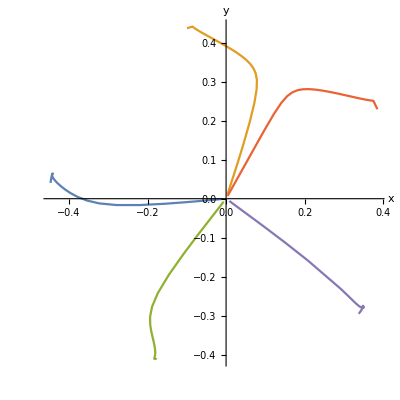

```mathematica
ParametricPlot[Evaluate[Table[{Subscript[x, i][t],Subscript[y, i][t]},{i,nsp}]/.sol],{t,0,tmax},PlotRange->All,AspectRatio->1,AxesLabel->{x,y}]
```

```mathematica
Show[
Plot3D[{Evaluate[Inv[FinalSlice[sol]]],0},{Subscript[x, 0],-1,1},{Subscript[y, 0],-1,1},MeshFunctions->{#3&},Mesh->{40,False},PlotPoints->50,PlotStyle->{Orange,{Black,Opacity[0.2]}},AxesLabel->{Subscript[x, 0],Subscript[y, 0],inv}],
ListPointPlot3D[Table[{Subscript[x, i],Subscript[y, i],0},{i,nsp}]/.FinalSlice[sol],PlotStyle->{Green,PointSize[0.03]}],
PlotRange->{-0.1,All}
]
```

-Graphics3D-

```mathematica
GlobalESSQ[FinalSlice[sol]]
```

{{False},{{0.000250588,{x→0.449575,y→-0.0408229}}}}

Looks like more than five species are needed here...

More About

Related Tutorials

ExampleModels

Related Wolfram Education Group Courses